```mathematica
DualDiagram[λ_] := Total /@ Transpose[
     (PadRight[#1, λ[[1]]] & ) /@ 
      (ConstantArray[1, #1] & ) /@ λ]; 
ToYD[stb_]:=Length/@stb;
CheckStandard[λT_] := 
   And @@ Flatten[{Table[λT[[a - 1,s]] < 
        λT[[a,s]], {a, 2, Length[λT]}, 
       {s, 1, Length[λT[[a]]]}], 
      Table[λT[[a,s - 1]] < λT[[a,s]], 
       {a, 1, Length[λT]}, {s, 2, 
        Length[λT[[a]]]}], Sort[Flatten[λT]] == 
       Range[Length[Flatten[λT]]], 
      ListQ /@ λT}];
```

```mathematica
GenerateQsystem[λ_]:=Block[{},
((* Length of spin chain *)
Len=Total[λ];
Unprotect[M];ClearAll[M];(* Unprotecting because of conflict with Combinatorica package *)
(* domain of interest is the values of {a,s} for which we are going to check QQ relation with Q[a,s] in the top left corner (smallest a,s)
FullYoungDiagram - is maximal possible domain of interest*)
FullYoungDiagram=Block[{mm},Flatten@Table[mm[a,s],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}]/.mm->List];
DomainOfInterest=FullYoungDiagram;
(* comment below provides some example of non-standard DomainOfInterest *)
(*DomainOfInterest=Block[{mm},Flatten@Table[mm[a,s],{a,0,1},{s,0,1}]/.mm->List];*)
M[a_,s_,YD_]:=M[a,s,YD]=Total[YD]+a s-Total[YD[[1;;a]]]-Total[DualDiagram[YD][[1;;s]]];
YQa[0,0,YD_]:=u^Total[YD]+Sum[u^(Total[YD]-k)sym[k],{k,Len}];
YQa[a_,s_,YD_]:=u^M[a,s,YD]+Sum[c[a,s,k] u^(M[a,s,YD]-k),{k,M[a,s,YD]}];
YQθ[0,0,YD_]:=YQa[0,0,YD];
YQθ[a_,s_,YD_]:=Product[u-qθ[a,s,k],{k,1,M[a,s,YD]}];
QQrel[a_,s_,YD_]:=
CoefficientList[(YQa[a,s,YD]/.u->u+I/2)(YQa[a+1,s+1,YD]/.u->u-I/2)-(YQa[a,s,YD]/.u->u-I/2)(YQa[a+1,s+1,YD]/.u->u+I/2)-I(M[a,s,YD]-M[a+1,s+1,YD])YQa[a+1,s,YD]YQa[a,s+1,YD],u]//(#/.Complex[0,b_]:>b)&;
Allrel=Monitor[Table[If[MemberQ[DomainOfInterest,{a,s}]&&M[a,s,λ]>0,QQrel[a,s,λ],Nothing],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}],{a,s}]//Flatten;
(* vars have coefficients of all Q-functions *)
vars=Table[If[a+s==0,Nothing,c[a,s,k]],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1},{k,M[a,s,λ]}]//Flatten;
(* only those appearing in domain of interest *)
vars2=DeleteCases[Variables[Allrel],sym[_]];
)
];
```

```mathematica
initθrep[λT_] := initθrep[λT] = 
   Block[{kk, sd}, kk[_, _] = 0; sd[m_] := 
      (Select[#1, #1 <= m & ] & ) /@ λT; 
     If[CheckStandard[λT], 
      Sort[Flatten[Table[Table[If[True || 
            MemberQ[DomainOfInterest, {a2, s2}], 
           qθ[a2, s2, ++kk[a2, s2]] -> 
            Product[(Length[sd[λT[[a,s]]][[a3]]] + a - 
                s - a3)/(Length[sd[λT[[a,s]]][[a3]]] + 
                a - s - a3 + 1), {a3, 1, a2}]*
             Product[(DualDiagram[Length /@ sd[λT[[a,
                   s]]]][[s3]] + s - a - s3)/(
                DualDiagram[Length /@ sd[λT[[a,s]]]][[
                 s3]] + s - a - s3 + 1), {s3, 1, s2}]*
             θ[λT[[a,s]]], Nothing], {a2, 0, a - 1}, 
          {s2, 0, s - 1}], {a, 1, Length[λT]}, 
         {s, 1, Length[λT[[a]]]}]]], 
      Print["Not standard tableau"]; ]]
```

```mathematica
LargeΛExpansionUptdStart[λT_]:=Block[{λ,Len},λ=λT//ToYD;Len=Total[λ];
(ΛinitθrepUptd=initθrep[λT]/.θ[i_]:>If[i==(λT//Max),Λ,0];  (*The set of  qθ for the initial λT will be used here*)
fsymrepUptd=Table[sym[n]->Expand@Coefficient[Product[u,{i,Len-1}](u-Λ),u,Len-n],{n,Len}];
ftransitUptd=Solve[(Table[If[a+s==0||Not@MemberQ[vars2,c[a,s,1]],Nothing,CoefficientList[YQa[a,s,λ]-(YQθ[a,s,λ]/.ΛinitθrepUptd),u]],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}]//Flatten)==0,vars2][[1]];
anlyticUptd=Collect[(Allrel/.fsymrepUptd/.c[a_,s_,k_]:>(c[a,s,k]+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,maxord}])/.ftransitUptd)//Expand,Λ];
);
];

LargeΛExpansionUptdInterim[λTcurrent_,λTlast_,solninterim_]:=Block[{λcurrent,λlast,Len},λcurrent=λTcurrent//ToYD;λlast=λTlast//ToYD;Len=Total[λcurrent];
((*The set of  qθ for the current λT---having removed some boxes*)
ΛinitθrepUptd=initθrep[λTcurrent]/.θ[i_]:>If[i==(λTcurrent//Max),Λ,0]; 
fsymrepUptd=Table[sym[n]->Expand@Coefficient[Product[u,{i,Len-1}](u-Λ),u,Len-n],{n,Len}];
ftransitUptdInterim=Solve[(Table[If[a+s==0||Not@MemberQ[vars2,c[a,s,1]],Nothing,CoefficientList[YQa[a,s,λcurrent]-If[a<Position[λTcurrent,λTcurrent//Max][[1,1]]&&s<Position[λTcurrent,λTcurrent//Max][[1,2]],(u-Sum[qθ[a,s,k],{k,M[a,s,λcurrent]}])YQa[a,s,λlast]/.solninterim/.ΛinitθrepUptd,YQa[a,s,λlast]/.solninterim/.ΛinitθrepUptd],u]],{a,0,Length[λcurrent]-1},{s,0,λcurrent[[a+1]]-1}]//Flatten)==0,vars2][[1]];
anlyticUptdInterim=Collect[(Allrel/.fsymrepUptd/.(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord}])))//Expand,Λ];
(*anlyticUptdInterim=Collect[(Allrel/.fsymrepUptd/.(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(-ord+1),{ord,1,maxord}]/.If[Exponent[If[x===0,1,x],Λ]==0,ecc[1][a,s,k]->0,{}])))//Expand,Λ];*)
(*propord=GroupBy[ftransitUptdInterim/.(c[a_,s_,k_]->x_):>({{a,s},Exponent[If[(x//Chop)===0,1,x],Λ]}),First];
propord=AssociationThread[propord//Keys,Min/@(propord//Values)[[All,All,2]]];
anlyticUptdInterim=Collect[(Allrel/.fsymrepUptd/.(ftransitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ^(propord[{a,s}]-ord),{ord,1,maxord}])))//Expand,Λ];*)
);
];
```

```mathematica
(*SubleadingOrdersUptdStart:=Block[{},
(subleadUptd=Monitor[Table[Normal@Series[anlyticUptd[[k]],{Λ,∞,maxord}],{k,Length[anlyticUptd]}],k];
cutoff=Series[Λ,{Λ,∞,maxord-1}]-Λ;
subleadingeqnsUptd=Monitor[Table[(subleadUptd[[k]]+cutoff)[[3]],{k,Length[subleadUptd]}],k];
Do[Λsol[ord]=Solve[subleadingeqnsUptd[[All,ord]]==0/.Flatten@Table[Λsol[k],{k,ord-1}],vars2/.c[a_,s_,k_]:>ecc[ord][a,s,k]][[1]],{ord,maxord}];
;)
]

SubleadingOrdersUptdInterim:=Block[{Λsolprov,varleft},
(subleadUptd=Monitor[Table[Normal@Series[(#/Λ^Exponent[#,Λ])&[anlyticUptdInterim[[k]]],{Λ,∞,maxord}],{k,Length[anlyticUptdInterim]}],k];
cutoff=Series[Λ,{Λ,∞,maxord-2}]-Λ;
subleadingeqnsUptd=Table[(anlyticUptdInterim[[k]]+cutoff)[[3]],{k,Length[subleadUptd]}]//PadRight;
Λsolprov={};
varleft={};
Do[Module[{solprovprov},solprovprov={};
Do[AppendTo[solprovprov,Solve[(subleadingeqnsUptd[[All,ord]][[i]]/.Λsolprov/.solprovprov//Chop)==0,Union[vars2/.c[a_,s_,k_]:>ecc[ord][a,s,k],varleft]][[1]]];solprovprov=(solprovprov//Flatten)/.(ecc[ord_][a_,s_,k_]->x_):>(ecc[ord][a,s,k]->(x/.(solprovprov//Flatten))),{i,Length[subleadingeqnsUptd[[All,ord]]]}];AppendTo[Λsolprov,solprovprov];
Λsolprov=(Λsolprov//Flatten)/.(ecc[ord_][a_,s_,k_]->x_):>(ecc[ord][a,s,k]->(x/.(Λsolprov//Flatten)));varleft=Complement[Union[vars/.c[a_,s_,k_]:>ecc[ord][a,s,k],varleft],Λsolprov//Keys]],{ord,maxord}];
(*Do[AppendTo[Λsolprov,Solve[(subleadingeqnsUptd[[All,ord]]/.Λsolprov//Chop)==0,Union[vars2/.c[a_,s_,k_]:>ecc[ord][a,s,k],varleft]][[1]]//Chop];
Λsolprov=(Λsolprov//Flatten);varleft=Complement[Union[vars/.c[a_,s_,k_]:>ecc[ord][a,s,k],varleft],Λsolprov//Keys],{ord,maxord}];*)
Λsolinterim=Λsolprov/.(ecc[ord_][a_,s_,k_]->x_):>(ecc[ord][a,s,k]->(x/.Λsolprov));
solnorder=Union[((If[RealValuedNumberQ[#//Values]==False,#,Nothing]&/@Λsolinterim)//Keys)/.(ecc[ord_][a_,s_,k_]:>ord-1),{maxord},varleft/.(ecc[ord_][a_,s_,k_]:>ord-1)]//Min;
(*Λsolinterim=FindMinimum[subleadingeqnsUptd^2//Chop//Flatten//Total,{#,0}&/@Variables[subleadingeqnsUptd//Chop]][[2]];*)
;)
]*)
```

```mathematica
(* generating equations using asymptotic approximation *)
AsymEqnsUptdStart[Λ0_]:=Block[{},
symrepUptd=fsymrepUptd/.Λ->Λ0;
transitUptd=ftransitUptd/.Λ->Λ0;
(*subnc=
Thread[Rule[vars,vars/.(c[a_,s_,k_]:>(c[a,s,k]+Sum[Λ0^(-ord+1)(ecc[ord][a,s,k]/.Λsol[ord]),{ord,maxord}]))/.transitUptd]];*)
subnc=transitUptd;
#/(1+Abs[#/.c[a_,s_,k_]:> (c[a,s,k]/.subnc)])&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand
];

AsymEqnsUptdInterim[Λ0_]:=Block[{},
symrepUptd=fsymrepUptd/.Λ->Λ0;
transitUptdInterim=ftransitUptdInterim/.Λ->Λ0;
(*subnc=
Thread[Rule[vars,vars/.(c[a_,s_,k_]:>(c[a,s,k]+Sum[Λ0^(-ord+1)(ecc[ord][a,s,k]/.Λsolinterim),{ord,solnorder}]))/.transitUptdInterim]];*)
(*subnc=
transitUptdInterim/.(c[a_,s_,k_]->x_):>(c[a,s,k]->x+Sum[ecc[ord][a,s,k] Λ0^(-ord+1),{ord,1,solnorder}]/.If[Exponent[If[x===0,1,x],Λ]==0,ecc[1][a,s,k]->0,{}])/.Λsolinterim;*)
subnc=transitUptdInterim;
#/(1+Abs[#/.c[a_,s_,k_]:> (c[a,s,k]/.subnc)])&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand
];

(* generating equations using previous order results and polynomial fit *)
InterpEqnsUptd[Λ0_]:=Block[{minterpord=Min[Length[Λvals]-1,interpord]},
symrepUptd=fsymrepUptd/.Λ->Λ0;
subnc=
Thread[Rule[vars,Round[Sum[(vars/.sol[Λvals[[-j]]])Product[If[j==j2,1,(Λ0-Λvals[[-j2]])/(Λvals[[-j]]-Λvals[[-j2]])],{j2,minterpord}],{j,minterpord}],10^-prec]]];
#/(#/.c[a_,s_,k_]:> ((1+Round[Random[]/100,10^-5])c[a,s,k]/.subnc))&/@(Allrel/.symrepUptd/.Λ->Λ0)//Expand
];
(* Routine to produce solution *)
FindSolUptd:=(i=0;interstep={};{minim,minsolrep}=FindMinimum[normedrel.normedrel,{vars,vars/.subnc}//Transpose,(*WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,*)(*MaxIterations->50,*)Method->Automatic,EvaluationMonitor:>(AppendTo[interstep,vars])
(*,EvaluationMonitor:>(i++;norm=normedrel.normedrel//N;If[i>MyMaxIterations,Throw["Too big step"]])*)
];AppendTo[Steps,interstep]);
SilentFindSolUptd:=(i=0;interstep={};{minim,minsolrep}=FindMinimum[normedrel.normedrel,{vars,vars/.subnc}//Transpose,(*WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,*)
(*MaxIterations->50,*)Method->Automatic,EvaluationMonitor:>(AppendTo[interstep,vars])(*,EvaluationMonitor:>(i++;If[i>MyMaxIterations,Throw["Too big step"]])*)];AppendTo[Steps,interstep]);
```

```mathematica
(* generating first sample points for interpolation to work + some large Λ expressions *)
GenerateSolsFromAsymptoticsUptdStart:=Block[{},
Λvals0={};
rng=Join[Range[Λ0,Λ0+(startinterpord-1) 1/40,1/40]]//Flatten//Union//Sort//Reverse;
Monitor[Do[
normedrel=AsymEqnsUptdStart[Λ0];
FindSolUptd;
(*sol[Λ0]:=Thread[Rule[vars2,(vars2/.subc)(vars3/.minsolrep)]];*)
sol[Λ0]=minsolrep;
AppendTo[Λvals0,Λ0];
,{Λ0,rng}],Row@{"Current Λ is: ",Λ0//N}]
];

GenerateSolsFromAsymptoticsUptdInterim:=Block[{},
Λvals0={};
rng=Join[Range[Λ0,Λ0+(startinterpord-1) 1/40,1/40]]//Flatten//Union//Sort//Reverse;
Monitor[Do[
normedrel=AsymEqnsUptdInterim[Λ0];
FindSolUptd;
(*sol[Λ0]:=Thread[Rule[vars2,(vars2/.subc)(vars3/.minsolrep)]];*)
sol[Λ0]=minsolrep;
AppendTo[Λvals0,Λ0];
,{Λ0,rng}],Row@{"Current Λ is: ",Λ0//N}]
];
```

```mathematica
(* Iteration procedure *)
IterateUptd[SYT_]:=Block[{},
pp=pmin;qq=1;
step:=qq/base^pp;
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,If[step<10^-20,Print[{SYT,step//N,Λvals//N}];Break[],
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqnsUptd[Λnew];
Which[
Catch[SilentFindSolUptd]==="Too big step",
pp=pp+1,
i>5,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew]
,
True,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
If[pp>pmin,qq=qq+Δq;If[qq==base,qq=1;pp=pp-1]];
];
ΛLast=Λvals[[-1]];
]],
Row@{"Current Λ history is: ",Λvals//N,"current Λ is: ",ΛLast//N, "   step is: ",step//N}];
];
```

```mathematica
SolutionFromSYTUptdStart[SYT_]:=Block[{λTstart,λstart},
(*Solve the initial YT---one row with increasing tableau values*)
Steps={};
λTstart=SYT;
λstart=λTstart//ToYD;
GenerateQsystem[λstart];
LargeΛExpansionUptdStart[λTstart];
(*SubleadingOrdersUptdStart;*)
GenerateSolsFromAsymptoticsUptdStart;
Λvals=Λvals0;
IterateUptd[λTstart];
]
SolutionFromSYTUptdInterim[SYTcurrent_,SYTlast_,solnlast_]:=Block[{λTinterim,λTlast,λinterim},
Steps={};
λTinterim=SYTcurrent;
λTlast=SYTlast;
λinterim=λTinterim//ToYD;
GenerateQsystem[λinterim];
LargeΛExpansionUptdInterim[λTinterim,λTlast,solnlast];
(*SubleadingOrdersUptdInterim;*)
GenerateSolsFromAsymptoticsUptdInterim;
Λvals=Λvals0;
IterateUptd[λTinterim];
]
SolutionFromSYTUptdStepwise[SYT_]:=Block[{λTlist},
StepsWholeIteration={};
ansWholeIteration={};
λTlist=Table[Select[MemberQ[Range[1,i],#]&]/@SYT/.{{}->Nothing},{i,Count[SYT[[1]]-Range[SYT[[1]]//Length],0],SYT//Max}][[2;;]];
SolutionFromSYTUptdStart[λTlist[[1]]];AppendTo[StepsWholeIteration,{Λvals[[#]],(Thread[vars->#]&)/@Steps[[#]]}&/@Range[Length[Steps]]];AppendTo[ansWholeIteration,{Λvals,sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0,λ]/.sol[Λvals[[#]]],u],{a,Length[λ]-1}])&/@Range[1,Length[Λvals]]}];
Do[SolutionFromSYTUptdInterim[λTlist[[i]],λTlist[[i-1]],sol[0]];AppendTo[StepsWholeIteration,{Λvals[[#]],(Thread[vars->#]&)/@Steps[[#]]}&/@Range[Length[Steps]]];AppendTo[ansWholeIteration,{Λvals,sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0,λ]/.sol[Λvals[[#]]],u],{a,Length[λ]-1}])&/@Range[1,Length[Λvals]]}];,{i,2,Length@λTlist}];
ansWholeIteration (*This prints all answers from all steps in the YT iteration (the last one can be called by ansWholeIteration[[-1]]); to get only the final answer, write: {Λvals,sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0,λ]/.sol[Λvals[[#]]],u],{a,Length[λ]-1}])&/@Range[1,Length[Λvals]]}*)
]
```

```mathematica
maxord=6;
startinterpord=3;
Λ0=2;
prec=MachinePrecision;
MyMaxIterations=12; 
interpord=40; 
base=2;pmin=5;RecoverySpeed=1/3;
Δq=(base-1)Min[1,RecoverySpeed];Λtarget=0;
```

pmin=0.75 jump
pmin=1 does not jump
Λ0=2 does not jump
Λ0=1 jumps
pmin=5 gives weird jumps in rig 20, among others.

Jumping starts to happen when a new solution for the next lambda value is exactly the same as the previous result. Due to failure to find a solution, so the old is returned again?

```mathematica
yd={4,2,1};
rigs=ModestoRiggedConfig[Total[yd],#]&/@ModesConfig[yd];
syts=ToSYT/@rigs;
```

```mathematica
StepsAllStepwise={};
lazyansStepwise=Module[{ans},ans=SolutionFromSYTUptdStepwise[#];AppendTo[StepsAllStepwise,StepsWholeIteration];ans]&/@syts;
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum::fmgz will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

FindMinimum::nrnum: The function value ComplexInfinity is not a real number at {c[1,0,1]} = {0.}.

Set::shape: Lists {minim,minsolrep} and FindMinimum[normedrel.normedrel,{,Method→Automatic] are not the same shape.

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

General::stop: Further output of FindMinimum::fmdig will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

FindMinimum::nrnum: The function value ComplexInfinity is not a real number at {c[0,1,1],c[0,1,2],c[0,2,1],c[1,0,1]} = {0.190044,-0.0668961,0.095022,-0.963481}.

Set::shape: Lists {minim,minsolrep} and FindMinimum[normedrel.normedrel,{,Method→Automatic] are not the same shape.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindMinimum::nrnum: The function value ComplexInfinity is not a real number at {c[1,0,1]} = {0.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

Set::shape: Lists {minim,minsolrep} and FindMinimum[normedrel.normedrel,{,Method→Automatic] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

FindMinimum::nrlnum: The function value {-4.95717×10^-8,-2.17287×10^-9,-6.18173×10^-9,1.79489×10^-9,Indeterminate,7.30022×10^-9} is not a list of real numbers with dimensions {6} at {c[0,1,1],c[0,1,2],c[1,0,1],c[1,0,2],c[1,1,1]} = {-0.734375,0.353,-0.734375,-0.186333,-0.367187}.

```mathematica
Table[RegionHausdorffDistance[Replace[x_:>{Re[x],Im[x]}]/@(lazyansStepwise[[All,-1,3,-1]][[i]]//Flatten),Replace[x_:>{Re[x]-1,Im[x]}]/@(lazyansCORRECT[[All,3,-1]][[i]]//Flatten)],{i,Length[lazyansCORRECT]}]//Chop
```

{0,0,0,0,0,0,0,0,0.865899,0,0,0,0,0,0,0,0.510818,0,0,0,0,0.255036,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
a=1;
Round[lazyansStepwise[[All,-1,3,-1]],10^-3]//N//Length
Round[lazyansStepwise[[All,-1,3,-1]],10^-3]//N//DeleteDuplicates//Length

repeats=If[#[[2]]>1,{#[[1]]//Flatten,Position[Round[lazyansStepwise[[All,-1,3,-1,a]],10^-3]//N,#[[1]]]//Flatten},Nothing]&/@Tally[Round[lazyansStepwise[[All,-1,3,-1,a]],10^-3]//N];
repeatlist=repeats[[All,2]]

showSYT/@ToSYT/@rigs[[#]]&/@repeatlist
```

35

35

{}

{}

```mathematica
Manipulate[{{lazyansStepwise[[rigg1,-1]][[1]],lazyansStepwise[[rigg1,-1]][[2]][[All,polno]]//Values}//Transpose,{lazyansStepwise[[rigg2,-1]][[1]],lazyansStepwise[[rigg2,-1]][[2]][[All,polno]]//Values}//Transpose}//ListPlot[#]&,{rigg1,1,Length[lazyansStepwise],1},{rigg2,1,Length[lazyansStepwise],1},{polno,1,Length[vars],1}]
```

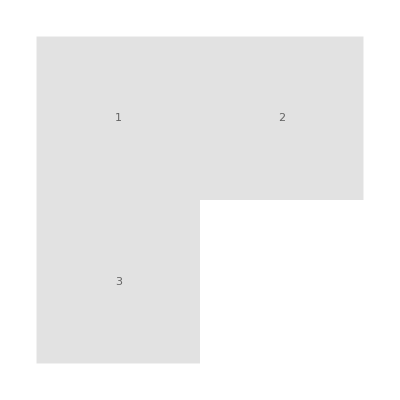
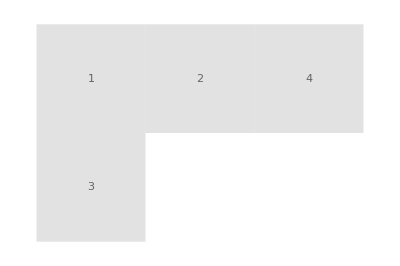
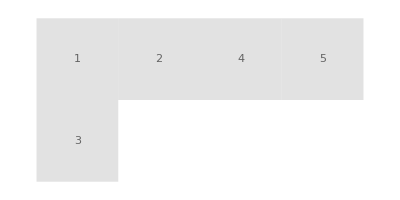
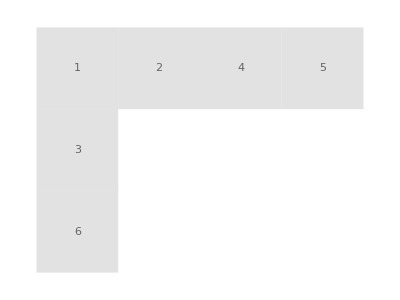
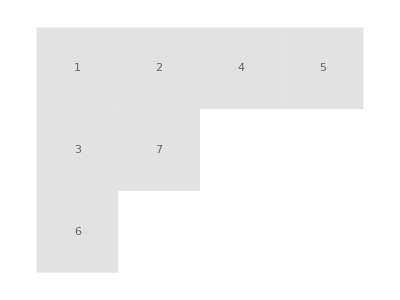
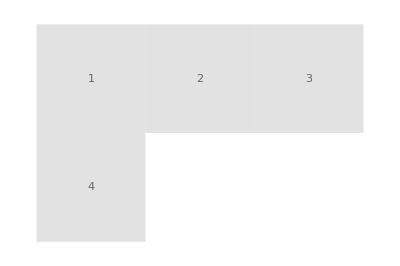
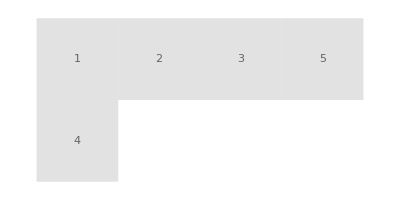
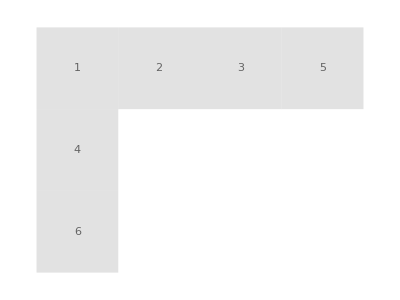

```mathematica
λTlist=Table[Select[MemberQ[Range[1,i],#]&]/@#/.{{}->Nothing},{i,Count[#[[1]]-Range[#[[1]]//Length],0],#//Max}][[2;;]]&/@{syts[[6]],syts[[9]]};
Map[showSYT,λTlist,{2}]
```

```mathematica
Manipulate[Column[Reverse@{({lazyansStepwise[[rigg1,-step1]][[1]],(lazyansStepwise[[rigg1,-step1]][[2]][[All,polno1]]//Values)-(lazyansStepwise[[rigg2,-step2]][[2]][[All,polno2]]//Values)}//Transpose)//ListPlot[#,ImageSize->Large,PlotRange->Automatic,PlotStyle->Gray]&,{{lazyansStepwise[[rigg1,-step1]][[1]],lazyansStepwise[[rigg1,-step1]][[2]][[All,polno1]]//Values}//Transpose,{lazyansStepwise[[rigg2,-step2]][[1]],lazyansStepwise[[rigg2,-step2]][[2]][[All,polno2]]//Values}//Transpose}//ListPlot[#,ImageSize->Large]&}],{rigg1,1,Length[lazyansStepwise],1},{rigg2,1,Length[lazyansStepwise],1},{step1,1,lazyansStepwise[[rigg1]]//Length,1},{step2,1,lazyansStepwise[[rigg2]]//Length,1},{polno1,1,Length[lazyansStepwise[[rigg1,-step1,2,1]]],1},{polno2,1,Length[lazyansStepwise[[rigg2,-step2,2,1]]],1}]
```

```mathematica
Manipulate[Show[({lazyansStepwise[[rig,-step]][[1]],lazyansStepwise[[rig,-step]][[2]][[All,polno]]//Values}//Transpose)//ListPlot[#]& ,Module[{},SubncStep[Λ0_,minterpord_]:=
Thread[Rule[vars,Round[Sum[(lazyansStepwise[[rig,-step]][[2]][[1;;interpfrom,polno]][[-j]]//Values)Product[If[j==j2,1,(Λ0-lazyansStepwise[[rig,-step]][[1]][[1;;interpfrom]][[-j2]])/(lazyansStepwise[[rig,-step]][[1]][[1;;interpfrom]][[-j]]-lazyansStepwise[[rig,-step]][[1]][[1;;interpfrom]][[-j2]])],{j2,minterpord}],{j,minterpord}],10^-prec]]];
{lazyansStepwise[[rig,-step]][[1]][[interpfrom+1;;]],(SubncStep[#,manyinterpor]&/@lazyansStepwise[[rig,-step]][[1]][[interpfrom+1;;]])[[All,polno]]//Values}//Transpose
]//ListLinePlot[#,PlotStyle->{Gray,Thinning}]&],{rig,1,Length[lazyansStepwise],1},{step,1,lazyansStepwise[[rig]]//Length,1},{polno,1,Length[lazyansStepwise[[rig,-step,2,1]]],1},{interpfrom,10,Length[lazyansStepwise[[rig,-step]][[1]]]-1,1},{manyinterpor,1,interpfrom-1,1}]
```

FilterRules::rep: 23.5038 is not a valid replacement rule.

FilterRules::rep: FilterRules[{{23.5038,0.102777,LegendMarkers→Automatic,Joined→Automatic,LabelStyle→{},Orientation→Column,AutoMarkers→{{False,Automatic}},AutoJoined→{False}}},Except[ListWrap|AutoMarkers|AutoJoined|Orientation]] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Join::heads: Heads List and FilterRules at positions 1 and 2 are expected to be the same.

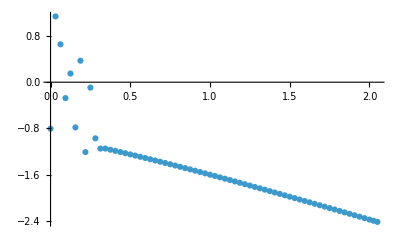

```mathematica
{lazyansStepwise[[22,-1]][[1]],lazyansStepwise[[22,-1]][[2]][[All,1]]//Values}//Transpose//ListPlot[#]&
```

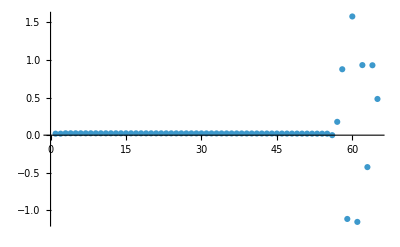

```mathematica
rig=22;
polno=1;
step=1;
Table[(lazyansStepwise[[rig,-step]][[2]][[i+1,polno]]//Values)-(lazyansStepwise[[rig,-step]][[2]][[i,polno]]//Values),{i,Length[lazyansStepwise[[rig,-step]][[2]]]-2}]//ListPlot[#,PlotRange->All]&
```

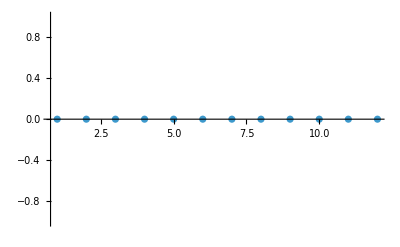

```mathematica
Table[(lazyansStepwise[[rig,-step]][[2]][[57,i]]//Values)-(lazyansStepwise[[rig,-step]][[2]][[56,i]]//Values),{i,Length[lazyansStepwise[[rig,-step]][[2,1]]]}]//ListPlot[#,PlotRange->All]&
```

```mathematica
probval=57;
Λ01=lazyansStepwise[[rig,-step]][[1]][[probval]];
λTlist=Table[Select[MemberQ[Range[1,i],#]&]/@syts[[rig]]/.{{}->Nothing},{i,Count[syts[[rig]][[1]]-Range[syts[[rig]][[1]]//Length],0],syts[[rig]]//Max}][[2;;]];
GenerateQsystem[λTlist[[-step]]//ToYD];
Len=λTlist[[-step]]//ToYD//Total;
fsymrepUptd=Table[sym[n]->Expand@Coefficient[Product[u,{i,Len-1}](u-Λ),u,Len-n],{n,Len}];
symrepUptd=fsymrepUptd/.Λ->Λ01;
ninterpord=Min[interpord,probval-1];
subnc=Thread[Rule[vars,Round[Sum[(lazyansStepwise[[rig,-step]][[2]][[1;;probval-1]][[-j]]//Values)Product[If[j==j2,1,(Λ01-lazyansStepwise[[rig,-step]][[1]][[1;;probval-1]][[-j2]])/(lazyansStepwise[[rig,-step]][[1]][[1;;probval-1]][[-j]]-lazyansStepwise[[rig,-step]][[1]][[1;;probval-1]][[-j2]])],{j2,ninterpord}],{j,ninterpord}],10^-prec]]];
normedrel=#/(#/.c[a_,s_,k_]:> ((1+Round[Random[]/100,10^-5])c[a,s,k]/.subnc))&/@(Allrel/.symrepUptd/.Λ->Λ01)//Expand;

SilentFindSolUptd:=(i=0;{minim,minsolrep}=FindMinimum[normedrel.normedrel,{vars,vars/.subnc}//Transpose,(*WorkingPrecision->MachinePrecision,PrecisionGoal->Automatic,AccuracyGoal->Automatic,*)(*MaxIterations->50,*)Method->Automatic(*,EvaluationMonitor:>(i++;
If[i>MyMaxIterations,Throw["Too big step"]])*)]);
SilentFindSolUptd[[2]]
```

{c[0,1,1]→-1.1283,c[0,1,2]→0.388669,c[0,1,3]→-0.0576351,c[0,1,4]→-0.0802687,c[0,2,1]→-0.579375,c[0,2,2]→-0.210269,c[0,3,1]→-0.289687,c[1,0,1]→0.556558,c[1,0,2]→-0.260652,c[1,0,3]→0.00148114,c[1,1,1]→-0.266847,c[2,0,1]→0.637885}

```mathematica
lazyansStepwise[[rig,-step]][[2]][[probval-1]]
```

{c[0,1,1]→-1.14787,c[0,1,2]→0.402016,c[0,1,3]→-0.0600621,c[0,1,4]→-0.0809631,c[0,2,1]→-0.589478,c[0,2,2]→-0.208993,c[0,3,1]→-0.294739,c[1,0,1]→0.54475,c[1,0,2]→-0.266741,c[1,0,3]→0.00232622,c[1,1,1]→-0.271428,c[2,0,1]→0.634595}

```mathematica
StepsAllStepwise[[rig,-step]][[57]]
```

{5/16,{}}